```mathematica
ClearAll;
SetDirectory[NotebookDirectory[]];
```

```mathematica
SensorLinB1r[g_] := Module[{mmIni,mmIniPairs,gn1,nodesp, nodesn,temp,temp2, gbipartite,maxmatching, gml,  NumberOfNodes, sensors, sensorswhere, sensorslin},
mmIni =FindIndependentEdgeSet[Graph[RandomSample[EdgeList[g]]]];
mmIniPairs=Partition[mmIni,1]/.{x_-> y_}->{x,y};
gn1 = EdgeDelete[g,mmIni];
nodesp=ToString[#]<>"p"&/@VertexList[gn1]; 
nodesn=ToString[#]<>"n"&/@VertexList[gn1];
(* create edges for the bipartite graph, e.g., 1->2 corresponds to 1p <-> 1n *)
temp=Partition[EdgeList[gn1],1]/.{x_-> y_}->{x,y} ;
temp2={ToString[#[[1]]]<>"p",ToString[#[[2]]]<>"n"}&/@temp;
gbipartite=Graph[Join[Join[RandomSample[nodesp], RandomSample[nodesn]]],Flatten[temp2/.{x_,y_}->{x<->y}] , VertexLabels->"Name", GraphLayout->"BipartiteEmbedding"]; 
maxmatching=FindIndependentEdgeSet[gbipartite];
gml=VertexList[Graph[maxmatching]];
NumberOfNodes=VertexCount[gn1];sensorswhere=Table[FreeQ[gml,ToString[i]<>"p" ],{i,1,NumberOfNodes}];sensorslin=Flatten[Position[sensorswhere,True]];
sensors = If[Length[sensorslin]==0, RandomInteger[{1,NumberOfNodes}],sensorslin]; 
sensors
]
```

```mathematica
(*swarmplot*)
intervalInverse[Interval[]]:=Interval[{-Infinity,Infinity}]
intervalInverse[Interval[int__]]:=Interval@@Partition[Replace[Flatten[{int}],{{-Infinity,mid___,Infinity}:>{mid},{-Infinity,mid__}:>{mid,Infinity},{mid__,Infinity}:>{-Infinity,mid},{mid___}:>{-Infinity,mid,Infinity}}],2]

intervalComplement[a_Interval,b__Interval]:=IntervalIntersection[a,intervalInverse@IntervalUnion[b]]
(*data is assumed to be a sorted vector of numbers*)beeswarm[data_,radius_]:=Module[{points,left,right,int},points={};
Do[int=Interval@@Cases[points,{x_,y_}/;y>pt-radius:>x+{-1,1} Sqrt[radius^2-(pt-y)^2]];
right=Min[intervalComplement[Interval[{0,Infinity}],int]];
left=Max[intervalComplement[Interval[{-Infinity,0}],int]];
AppendTo[points,{If[right<-left,right,left],pt}],{pt,data}];
points]
Options[beeswarmPlot]=Join[Options[Graphics],{PlotStyle->Automatic}];

SetOptions[beeswarmPlot,Frame->True];
SetOptions[beeswarmPlot,FrameTicks->{None,Automatic}];

beeswarmPlot[data_?(VectorQ[#,NumericQ]&),radius:(_?NumericQ|Automatic):Automatic,opt:OptionsPattern[]]:=beeswarmPlot[{data},radius,opt]
beeswarmPlot[data:{__?(VectorQ[#,NumericQ]&)},radius:(_?NumericQ|Automatic):Automatic,opt:OptionsPattern[]]:=Module[{r,order,flatData,colours,colfun},(*generate colour indices and sort them together with the data*)flatData=Flatten[data];
order=Ordering[flatData];
colours=Flatten@Table[ConstantArray[i,Length[data[[i]]]],{i,Length[data]}];
flatData=flatData[[order]];
colours=colours[[order]];
(*automatic radius selection*)r=If[radius===Automatic,4 Mean@Differences[flatData],2 radius];
(*handle the PlotStyle option*)colfun=With[{ps=OptionValue[PlotStyle]},Switch[ps,Automatic,ColorData[1],_List,Function[i,ps[[Mod[i,Length[ps],1]]]],_,ps&]];
(*call the packing function and build the graphics using the result*)Graphics[MapThread[{colfun[#2],Disk[#1,0.95 r/2]}&,{beeswarm[flatData,r],colours}],Sequence@@FilterRules[{opt},Options[Graphics]],Frame->OptionValue[Frame],FrameTicks->OptionValue[FrameTicks]]]
```

```mathematica
(*plot parameters*)
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
SwarmCol = {"#94c33a","#9952df","#dc7124","#593193","#56b16c","#cf5aba","#657ade","#aa9040","#bc002d","#8686ce","#7d3f00"};
```

```mathematica
fnS = {"M_SD_001","M_SD_002","M_SD_003","M_SD_008","M_SD_009","M_SD_011","M_SD_014","M_SD_015","M_SD_017","M_SD_021","M_SD_023","M_SD_031","M_SD_032","M_SD_033","M_SD_010","M_SD_012","M_SD_013","M_SD_020","M_SD_024","M_SD_025","M_SD_026","M_SD_027","M_SD_028","M_SD_029","M_SD_030"};
fnP={"11sp_M_PL_069_03","22sp_M_PL_036","29sp_M_PL_069_01","36sp_M_PL_067","40sp_M_PL_032","49sp_M_PL_050","52sp_M_PL_071","57sp_M_PL_025","61sp_M_PL_003","68sp_M_PL_039","78sp_M_PL_006", "M_PL_008","M_PL_011","M_PL_013","M_PL_033","M_PL_037","M_PL_038","M_PL_046","M_PL_059","M_PL_063","M_PL_064","M_PL_065","M_PL_066","M_PL_068","M_PL_069_02","M_PL_070"};
fall = Join[fnS,fnP];
```

```mathematica
NonSensorColor=hexToRGB["#bf00bf"];
SensorColor=hexToRGB["#5db6be"];
MarkerSensor = Graphics[{SensorColor,Disk[]}];
MarkerNonSensor = Graphics[{NonSensorColor,Disk[]}];
```

## Import data

```mathematica
Ac=Table[Import["General_data/"<>fall[[i]]<>"_Ac.csv", "Table"],{i,1,Length[fall]}];
```

```mathematica
A=Table[AdjacencyGraph[Import["General_data/"<>fall[[i]]<>"_Abin.csv", "Table"]],{i,1,Length[fall]}];
G = Table[Graph[A[[i]]],{i,1,Length[fall]}];
```

```mathematica
OrderMostRepeat=Import["General_data/OrderRepeatSP.mx"];
Detect=Import["General_data/DetectSP.mx"];
Detect0=Import["General_data/DetectSP0.mx"];
SensorScore=Import["General_data/SensorsRepeatSP.mx"];

(*EW related*)
MaxEW =Table[Max[Detect[[i]]], {i,Length[SensorScore]}];
VarEW =Table[Variance[Detect[[i]]], {i,Length[SensorScore]}];
MedEW =Table[Median[Detect[[i]]], {i,Length[SensorScore]}];
MeanEW = Table[Mean[Detect[[i]]], {i,Length[SensorScore]}];
EWRel={
MaxEW,
VarEW,
MedEW ,
MeanEW 
};
LabelEW = {"MaxEW",
"VarEW",
"MedEW" ,
"MeanEW "};
(*sensor set related*)
SetSizeS = Import["General_data/NumberOfSensorsS.mx"];
SetSizeP = Import["General_data/NumberOfSensorsP.mx"];
SetSize = Join[SetSizeS, SetSizeP];
RelSetSize = N[Table[SetSize[[i]]/Length[Detect[[i]]],{i,Length[SetSize]}]];
MeanSS = Table[Mean[SensorScore[[i]]], {i,Length[SensorScore]}];
MedSS = Table[Median[SensorScore[[i]]], {i,Length[SensorScore]}];
MaxSS =Table[Max[SensorScore[[i]]], {i,Length[SensorScore]}];
VarSS =Table[Variance[SensorScore[[i]]], {i,Length[SensorScore]}];
ZscoreSS = Table[(SensorScore[[i]]-Mean[SensorScore[[i]]])/StandardDeviation[SensorScore[[i]]], {i,Length[SensorScore]}];
MeanZscoreSS = Table[Mean[Zscore[[i]]], {i,Length[SensorScore]}];
MaxZscoreSS = Table[1/Max[Zscore[[i]]], {i,Length[SensorScore]}];
SkewSS = Table[1/(Skewness[SensorScore[[i]]]),{i,Length[SensorScore]}];
Prop40SS = Table[1/(Length[Position[SensorScore[[i]],_?(#≤.4&)]]/Length[SensorScore[[i]]]),{i,Length[SensorScore]}];
SSRel = {
	       SetSize ,
	RelSetSize ,
	MeanSS ,
	MedSS ,
	MaxSS ,
	VarSS ,
	MeanZscoreSS ,
	       MaxZscoreSS,
SkewSS,
Prop40SS
	};
LabelSS={
	       "SetSize",
	"RelSetSize",
	"MeanSS",
"MedSS",
	"MaxSS",
"VarSS",
	"MeanZscoreSS",
	   "MaxZscoreSS",
"SkewSS",
"Prop40SS"};
(*graph related*)
NetSize= Table[Length[Detect[[i]]], {i,Length[SensorScore]}];
DegC = Table[DegreeCentrality[G[[i]]],{i,1,Length[fall]}];
VarDeg = Table[Variance[DegC[[i]]],{i,1,Length[fall]}];
MeanDeg = Table[1/Mean[DegC[[i]]],{i,1,Length[fall]}];
MedDeg = Table[1/Median[DegC[[i]]],{i,1,Length[fall]}];
SkewDeg  = Table[Skewness[DegC[[i]]],{i,1,Length[fall]}];
Connectance = Table[1/(EdgeCount[G[[i]]]/(VertexCount[G[[i]]])^2),{i,1,Length[fall]}];
AnPlantDisp =Flatten[ Import["General_data/an-pl_dispSP.csv","Table"]];
PropSp=Table[Length[Position[DegC[[i]],1]]/Length[DegC[[i]]],{i,1,Length[fall]}];
PropGen=Table[(1/(Length[Position[DegC[[i]],_?(#>= (Length[DegC[[i]]]/4)&)]]/Length[DegC[[i]]])),{i,1,Length[fall]}];
PropGen[[Flatten[Position[PropGen,ComplexInfinity]]]]=1;
PropVertMatch = Table[ 1/(Length[FindIndependentVertexSet[G[[i]]]]/VertexCount[G[[i]]]),{i,1,Length[fall]}];
PropEdgeMatch = Table[ 1/(Length[FindIndependentEdgeSet[G[[i]]]]/EdgeCount[G[[i]]]),{i,1,Length[fall]}];
(*{0.13367938156461184,-0.19889214343141912,0.157691999902914,0.31801219980420986,-0.3121147754175968,0.32409734176980926,0.3154131241662472,-0.3281876665048428,-0.13367938156461184,-0.08500595719260653}*)
GraphRel ={
NetSize,
MeanDeg,
VarDeg,
SkewDeg,
Connectance,
AnPlantDisp,
PropSp,
PropGen,
MedDeg
};
LabelGraph = {"NetSize",
"MeanDeg",
"VarDeg",
"SkewDeg",
"Connectance",
"AnPlantDisp",
"PropSp",
"PropGen",
"MedDeg"};
(*competition related*)
InterComp = Table[Total[Ac[[i]],{2}], {i,Length[SensorScore]}];
MeanInterComp =  Table[1/Mean[InterComp[[i]]], {i,Length[SensorScore]}];
MedInterComp = Table[1/Median[InterComp[[i]]], {i,Length[SensorScore]}];
SkewInterComp = Table[Skewness[InterComp[[i]]],{i,Length[SensorScore]}];
NonComp=Table[Length[Position[InterComp[[i]],0.]],{i,Length[SensorScore]}];
CompRel={
MeanInterComp,
MedInterComp ,
SkewInterComp,
NonComp
};
LabelComp = {"MeanInterComp",
"MedInterComp",
"SkewInterComp",
"NonComp"};


LabelTests = {

	"SetSize" ,
	"RelSetSize" ,
	"MeanSS ""MaxEW",
"VarEW",
"MedEW" ,
"MeanEW ",,
	"MedSS ",
	"MaxSS ",
	"VarSS ",
	"MeanZscoreSS ",
	       "MaxZscoreSS",
	"SkewSS",
	"Prop40SS",
"NetSize",
"MeanDeg",
"VarDeg",
"SkewDeg",
"Connectance",
"AnPlantDisp",
"PropSp",
"PropGen",
"MedDeg",
	"MeanInterComp",
	"MedInterComp ",
	"SkewInterComp",
	"NonComp"
};
```

Power::infy: Infinite expression 1/0 encountered.

```mathematica
Table[Export[LabelEW[[i]]<>".csv",N[EWRel[[i]]],"CSV"],{i,Length[EWRel]}]
```

{MaxEW.csv,VarEW.csv,MedEW.csv,MeanEW .csv}

```mathematica
Table[Export[LabelSS[[i]]<>".csv",N[SSRel[[i]]],"CSV"],{i,Length[SSRel]}]
```

{SetSize.csv,RelSetSize.csv,MeanSS.csv,MedSS.csv,MaxSS.csv,VarSS.csv,MeanZscoreSS.csv,MaxZscoreSS.csv,SkewSS.csv,Prop40SS.csv}

```mathematica
Table[Export[LabelGraph[[i]]<>".csv",N[GraphRel[[i]]],"CSV"],{i,Length[GraphRel]}]
```

{NetSize.csv,MeanDeg.csv,VarDeg.csv,SkewDeg.csv,Connectance.csv,AnPlantDisp.csv,PropSp.csv,PropGen.csv,MedDeg.csv}

```mathematica
Table[Export[LabelComp[[i]]<>".csv",N[CompRel[[i]]],"CSV"],{i,Length[CompRel]}]
```

{MeanInterComp.csv,MedInterComp.csv,SkewInterComp.csv,NonComp.csv}

## Best EW score for different ratios R_f

data

```mathematica
DetectMost10= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.1]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost15= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.15]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost20= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.2]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost25= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.25]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost30= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.3]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost35= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.35]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost40= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.4]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost45= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.45]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost50= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.5]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost55= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.55]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost60= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.6]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost65= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.65]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost70= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.7]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost75= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.75]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost80= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.8]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost85= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.85]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost90= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.9]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost95= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.95]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost100= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost105= Table[orderM = OrderMostRepeat[[i]][[1;;Ceiling[SetSize[[i]]*1.05]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost110= Table[orderM = OrderMostRepeat[[i]][[1;;Ceiling[SetSize[[i]]*1.1]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
```

```mathematica
DetectSizeProp = Table[
{Max[DetectMost10[[i]]],
Max[DetectMost15[[i]]],
Max[DetectMost20[[i]]],
Max[DetectMost25[[i]]],
Max[DetectMost30[[i]]],
Max[DetectMost35[[i]]],
Max[DetectMost40[[i]]],
Max[DetectMost45[[i]]],
Max[DetectMost50[[i]]],
Max[DetectMost55[[i]]],
Max[DetectMost60[[i]]],
Max[DetectMost65[[i]]],
Max[DetectMost70[[i]]],
Max[DetectMost75[[i]]],
Max[DetectMost80[[i]]],
Max[DetectMost85[[i]]],
Max[DetectMost90[[i]]],
Max[DetectMost95[[i]]],
Max[DetectMost100[[i]]],
Max[DetectMost105[[i]]],
Max[DetectMost110[[i]]]}/Max[Detect[[i]]],{i,Length[DetectMost10]}];
DelInf = Table[DeleteCases[DetectSizeProp[[All,i]],-∞],{i,1,21,2}];
DelInfo=DelInf;
Prop1 =Table[pos1=Flatten[Position[DelInf[[i]],_?(#>= 1&)]];
len = Length[pos1];
If[len>11,DelInf[[i]][[pos1[[11;;len]]]]=1.04];
If[len>22,DelInf[[i]][[pos1[[22;;len]]]]=1.08];
If[len>32,DelInf[[i]][[pos1[[32;;len]]]]=1.12];
len/Length[DelInf[[i]]],{i,11}];
```

```mathematica
N[Prop1]
```

{0.290323,0.333333,0.431818,0.521739,0.591837,0.632653,0.632653,0.632653,0.693878,0.745098,0.823529}

build plot

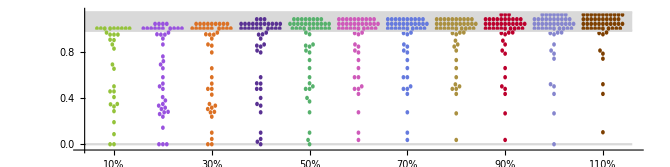

```mathematica
widthS =.02;
Bees=Graphics[{First@beeswarmPlot[DelInf[[1]],widthS,PlotStyle->hexToRGB[SwarmCol[[1]]]],Translate[First@beeswarmPlot[DelInf[[2]],widthS,PlotStyle->hexToRGB[SwarmCol[[2]]]],{0.5,0}],Translate[First@beeswarmPlot[DelInf[[3]],widthS,PlotStyle->hexToRGB[SwarmCol[[3]]]],{1,0}],
Translate[First@beeswarmPlot[DelInf[[4]],widthS, PlotStyle->hexToRGB[SwarmCol[[4]]]],{1.5,0}],
Translate[First@beeswarmPlot[DelInf[[5]],widthS, PlotStyle->hexToRGB[SwarmCol[[5]]]],{2,0}],
Translate[First@beeswarmPlot[DelInf[[6]],widthS,PlotStyle->hexToRGB[SwarmCol[[6]]]],{2.5,0}],
Translate[First@beeswarmPlot[DelInf[[7]],widthS,PlotStyle->hexToRGB[SwarmCol[[7]]]],{3,0}],
Translate[First@beeswarmPlot[DelInf[[8]],widthS,PlotStyle->hexToRGB[SwarmCol[[8]]]],{3.5,0}],
Translate[First@beeswarmPlot[DelInf[[9]],widthS,PlotStyle->hexToRGB[SwarmCol[[9]]]],{4,0}],
Translate[First@beeswarmPlot[DelInf[[10]],widthS,PlotStyle->hexToRGB[SwarmCol[[10]]]],{4.5,0}],
Translate[First@beeswarmPlot[DelInf[[11]],widthS,PlotStyle->hexToRGB[SwarmCol[[11]]]],{5,0}]
},Frame->False];
band2 = ListPlot[{{-.3,0},{5.3,0}},PlotStyle->{{LightGray}}, Joined->True];
band1= ListPlot[{{{-.3,.98},{5.3,.98}},{{-.3,1.14},{5.3,1.14}}},PlotStyle->{{LightGray}}, Joined->True,Filling-> {1->{{2},{Opacity[0.15
]}}},Ticks->{{{0,"10%"},{.5,"20%"},{1,"30%"},{1.5,"40%"},{2,"50%"},{2.5,"60%"},{3,"70%"},{3.5,"80%"},{4,"90%"},{4.5,"100%"},{5,"110%"}},{{0,"0.0"},{.2,".02"},{.4,"0.4"},{.6,"0.6"},{.8,"0.8"},{1.06,"1.0"}}},PlotRange->{{-.3,5.3},{-.05,1.15}}];
BeeSwarmAll = Show[band1,band2,Bees,AspectRatio->1/4,AxesOrigin->{-.3,-.05}]
```

# Non Rf vs network properties

## Correlations

```mathematica
Pval=.05
```

0.05

Including network 39

```mathematica
NetsI = Range[1,51]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51}

```mathematica
EWCorrI={Table[SpearmanRankTest[DelInfo[[10]][[NetsI]],EWRel[[i]][[NetsI]],"TestStatistic"],{i,Length[EWRel]}],
Table[SpearmanRankTest[DelInfo[[10]][[NetsI]],EWRel[[i]][[NetsI]],"PValue"],{i,Length[EWRel]}]}
SigEWI=Flatten[Position[EWCorrI[[2]],_?(#≤Pval&)]]
```

{{0.205538,0.308783,0.320699,0.354406},{0.147911,0.0274772,0.0217652,0.0107219}}

{2,3,4}

```mathematica
SSCorrI={Table[SpearmanRankTest[DelInfo[[10]][[NetsI]],SSRel[[i]][[NetsI]],"TestStatistic"],{i,Length[SSRel]}],
Table[SpearmanRankTest[DelInfo[[10]][[NetsI]],SSRel[[i]][[NetsI]],"PValue"],{i,Length[SSRel]}]}
SigSSI=Flatten[Position[SSCorr[[2]],_?(#≤Pval&)]]
```

{{0.224867,0.263011,0.266231,0.246749,0.262401,0.303348,0.102046,0.229549,-0.0218027,0.254003},{0.112637,0.0622254,0.0589757,0.0808882,0.0628566,0.0304719,0.476123,0.105149,0.879297,0.0720816}}

{6}

```mathematica
GraphCorrI={Table[SpearmanRankTest[DelInfo[[10]][[NetsI]],GraphRel[[i]][[NetsI]],"TestStatistic"],{i,Length[GraphRel]}],
Table[SpearmanRankTest[DelInfo[[10]][[NetsI]],GraphRel[[i]][[NetsI]],"PValue"],{i,Length[GraphRel]}]}
SigGraphI=Flatten[Position[GraphCorr[[2]],_?(#≤Pval&)]]
```

{{0.063676,0.158568,0.118054,0.236167,0.226595,0.237249,0.225866,0.319049,0.214278},{0.657104,0.266406,0.409336,0.0952265,0.109828,0.0936752,0.111006,0.0224908,0.131066}}

{8}

```mathematica
CompCorrI={Table[SpearmanRankTest[DelInfo[[10]][[NetsI]],CompRel[[i]][[NetsI]],"TestStatistic"],{i,Length[CompRel]}],
Table[SpearmanRankTest[DelInfo[[10]][[NetsI]],CompRel[[i]][[NetsI]],"PValue"],{i,Length[CompRel]}]}
SigCompI=Flatten[Position[CompCorr[[2]],_?(#≤Pval&)]]
```

{{-0.00206801,0.0738575,0.0669444,0.160789},{0.988509,0.6065,0.640678,0.259681}}

## ANOVA test

```mathematica
EWRelSigR=Table[EWRel[[SigEWI[[i]]]]/Max[EWRel[[SigEWI[[i]]]]],{i,Length[SigEWI]}];
EWPosL = Table[Flatten[Position[EWRelSigR[[i]],_?(#≤ .25&)]],{i,Length[EWRelSigR]}];
EWPosLM = Table[Flatten[Position[EWRelSigR[[i]],_?(.25<#≤ .5&)]],{i,Length[EWRelSigR]}];
EWPosLH = Table[Flatten[Position[EWRelSigR[[i]],_?(.5<#≤ .75&)]],{i,Length[EWRelSigR]}];
EWPosH = Table[Flatten[Position[EWRelSigR[[i]],_?(#> .25&)]],{i,Length[EWRelSigR]}];
```

```mathematica
EWPosL
```

{{4,5,7,8,9,11,14,15,17,19,22,23,27,28,30,31,33,34,39,41,43,46,48,51},{16,22,27,39,48},{48}}

```mathematica
Low=Table[pp=EWPosL[[i]][[j]];
{i,1,DelInfo[[10]][[pp]]},{i,Length[EWPosL]},{j,Length[EWPosL[[i]]]}];
```

```mathematica
LowMed = Table[pp=EWPosLM[[i]][[j]];
{i,2,DelInfo[[10]][[pp]]},{i,Length[EWPosLM]},{j,Length[EWPosLM[[i]]]}];
```

```mathematica
High=Table[pp=EWPosH[[i]][[j]];
{i,1,DelInfo[[10]][[pp]]},{i,Length[EWPosH]},{j,Length[EWPosH[[i]]]}];
```

```mathematica
HighMed = Table[pp=EWPosLH[[i]][[j]];
{i,2,DelInfo[[10]][[pp]]},{i,Length[EWPosLH]},{j,Length[EWPosLH[[i]]]}];
```

```mathematica
ANOVA[Join[LowMed[[2]],LowMed[[3]],Low[[2]],Low[[3]],HighMed[[2]],HighMed[[3]],High[[2]],High[[3]]],{x,y,All},{x,y},PostTests -> {Tukey,Bonferroni}]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
x | 1 | 0.00234416 | 0.00234416 | 0.0508197 | 0.8219
y | 1 | 0.00969713 | 0.00969713 | 0.210227 | 0.647146
x y | 1 | 0.00302635 | 0.00302635 | 0.065609 | 0.798135
Error | 179 | 8.25674 | 0.0461271 |  | 
Total | 182 | 8.27181 |  |  | ,CellMeans→All | 0.91026
x[2] | 0.91382
x[3] | 0.906662
y[1] | 0.916728
y[2] | 0.902116
x[2] y[1] | 0.916728
x[2] y[2] | 0.910203
x[3] y[1] | 0.916728
x[3] y[2] | 0.893828,PostTests→{x→Bonferroni | {}
Tukey | {},y→Bonferroni | {}
Tukey | {}}}

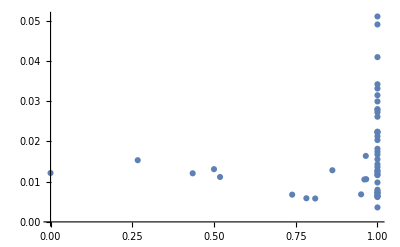
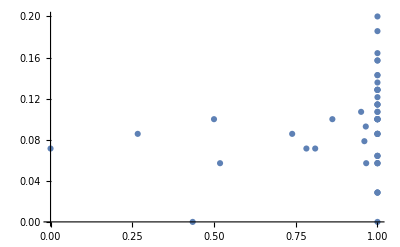
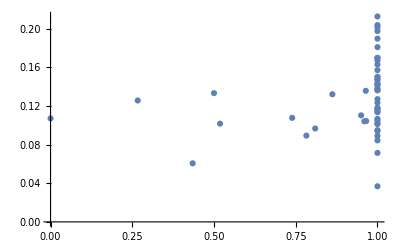

{MaxEW.csv,VarEW.csv,MedEW.csv,MeanEW .csv}

```mathematica
Table[ListPlot[Transpose@{DelInfo[[10]],EWRel[[SigEWI[[i]]]]}],{i,Length[SigEWI]}]
Table[Export[LabelEW[[i]]<>".csv",N[EWRel[[i]]],"CSV"],{i,Length[EWRel]}]
```

```mathematica
Export[ "Rf.csv",N[DelInfo[[10]]]]
```

Rf.csv

```mathematica
Length[LabelSS]
```

7

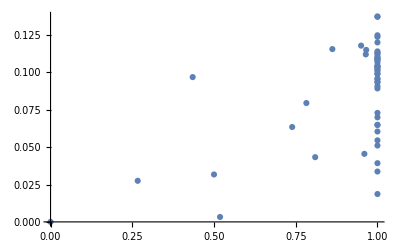

Part::partw: Part 8 of {MedSS ,MaxSS ,VarSS ,MeanZscoreSS ,MaxZscoreSS,SkewSS,Prop40SS} does not exist.

StringJoin::string: String expected at position 1 in {MedSS ,MaxSS ,VarSS ,MeanZscoreSS ,MaxZscoreSS,SkewSS,Prop40SS}⟦8⟧<>.csv.

Export::chtype: First argument {MedSS ,MaxSS ,VarSS ,MeanZscoreSS ,MaxZscoreSS,SkewSS,Prop40SS}⟦8⟧<>.csv is not a valid file specification.

Part::partw: Part 9 of {MedSS ,MaxSS ,VarSS ,MeanZscoreSS ,MaxZscoreSS,SkewSS,Prop40SS} does not exist.

StringJoin::string: String expected at position 1 in {MedSS ,MaxSS ,VarSS ,MeanZscoreSS ,MaxZscoreSS,SkewSS,Prop40SS}⟦9⟧<>.csv.

Export::chtype: First argument {MedSS ,MaxSS ,VarSS ,MeanZscoreSS ,MaxZscoreSS,SkewSS,Prop40SS}⟦9⟧<>.csv is not a valid file specification.

Part::partw: Part 10 of {MedSS ,MaxSS ,VarSS ,MeanZscoreSS ,MaxZscoreSS,SkewSS,Prop40SS} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in {MedSS ,MaxSS ,VarSS ,MeanZscoreSS ,MaxZscoreSS,SkewSS,Prop40SS}⟦10⟧<>.csv.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Export::chtype: First argument {MedSS ,MaxSS ,VarSS ,MeanZscoreSS ,MaxZscoreSS,SkewSS,Prop40SS}⟦10⟧<>.csv is not a valid file specification.

General::stop: Further output of Export::chtype will be suppressed during this calculation.

{MedSS .csv,MaxSS .csv,VarSS .csv,MeanZscoreSS .csv,MaxZscoreSS.csv,SkewSS.csv,Prop40SS.csv,$Failed,$Failed,$Failed}

```mathematica
Table[ListPlot[Transpose@{DelInfo[[10]],SSRel[[SigSSI[[i]]]]}],{i,Length[SigSSI]}]
Table[Export[LabelSS[[i]]<>".csv",N[SSRel[[i]]],"CSV"],{i,Length[SSRel]}]
```

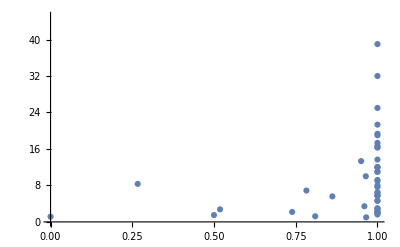

{PropGen.csv}

```mathematica
Table[ListPlot[Transpose@{DelInfo[[10]],GraphRel[[SigGraphI[[i]]]]}],{i,Length[SigGraphI]}]
Table[Export[LabelGraph[[SigGraphI[[i]]]]<>".csv",N[GraphRel[[SigGraphI[[i]]]]],"CSV"],{i,Length[SigGraphI]}]
```

## Covariance Matrices

## Matrix Plot All together

```mathematica
SigPosAllI=Flatten[Join[SigEWI, SigSSI+Length[EWCorrI[[2]]],{ SigGraphI+(Length[EWCorrI[[2]]]+Length[SSCorrI[[2]]])}]];
```

```mathematica
OrderRfAll = Ordering[DelInfo[[10]]]
```

{51,6,39,21,7,9,17,4,1,30,14,49,34,2,3,10,12,16,32,36,37,42,45,47,23,19,28,46,5,8,11,15,48,22,26,27,33,24,41,50,31,13,43,35,38,44,20,25,29,40,18}

```mathematica
OrderRfI = OrderRfAll;
```

```mathematica
MatValAll = Join[Table[EWRel[[i]][[OrderRfAll]]/Max[EWRel[[i]]],{i,Length[EWRel]}],
Table[SSRel[[i]][[OrderRfAll]]/Max[SSRel[[i]]],{i,Length[SSRel]}],
Table[GraphRel[[i]][[OrderRfAll]]/Max[GraphRel[[i]]],{i,Length[GraphRel]}],
Table[CompRel[[i]][[OrderRfAll]]/Max[CompRel[[i]]],{i,Length[CompRel]}]
];
LabelsT = Thread[{Range[Length[LabelTests]],LabelTests}];

MatrixPlot[MatValAll, ColorFunction->"ThermometerColors",ColorFunctionScaling->False,FrameTicks->{LabelsT,Automatic},PlotLegends->Automatic]
```

-Graphics-

```mathematica
MatValAllp = Append[MatValAll,DelInfo[[10]][[OrderRfAll]]];
```

```mathematica
MatrixPlot[MatValAllp, ColorFunction->"ThermometerColors",ColorFunctionScaling->False,FrameTicks->{LabelsT,Automatic},PlotLegends->Automatic]
```

-Graphics-

```mathematica
PvalsAllI=Flatten[{EWCorrI[[2]],SSCorrI[[2]], GraphCorrI[[2]],CompCorrI[[2]]}];
MatrixPlot[Transpose[{PvalsAllI}],ColorFunction->Hue,PlotLegends->Automatic,FrameTicks->{LabelsT,Automatic}]
```

-Graphics-

Significant correlations

```mathematica
LabelsTI = Thread[{Range[Length[LabelTests[[SigPosAllI]]]],LabelTests[[SigPosAllI]]}];
```

```mathematica
MatValI = Join[
Table[SSRel[[i]][[OrderRfI]]/Max[SSRel[[i]][[NetsI]]],{i,SigSSI}],
Table[GraphRel[[i]][[OrderRfI]]/Max[GraphRel[[i]][[NetsI]]],{i,SigGraphI}]
];
```

```mathematica
MatValAddI = Join[
Table[Flatten[{SSRel[[i]][[OrderRfI]]/Max[SSRel[[i]][[NetsI]]]}],{i,SigSSI}],
Table[Flatten[{GraphRel[[i]][[OrderRfI]]/Max[GraphRel[[i]][[NetsI]]]}],{i,SigGraphI}]
];
```

```mathematica
SigPosAllI[[Length[SigEWI]+1;;]]
```

{6,7,8,9,10,14,18,20,22}

```mathematica
LabelsTI = Thread[{Range[9],LabelTests[[SigPosAllI[[Length[SigEWI]+1;;]]]]}];
```

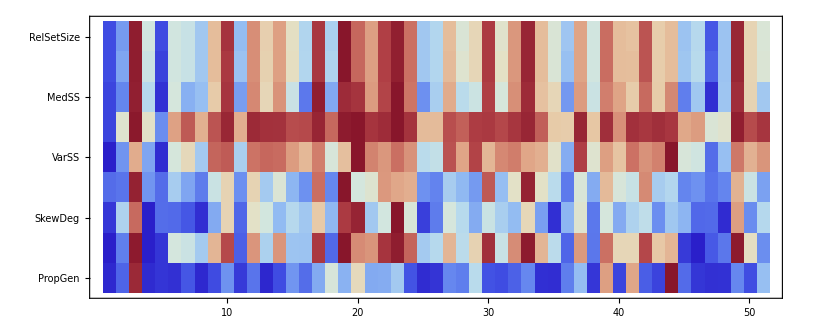

```mathematica
MatrixPlot[MatValI, ColorFunction->"ThermometerColors",ColorFunctionScaling->False, FrameTicks->{LabelsTI, Automatic}]
```

Adding sum and Rf

```mathematica
SumValI = Total[MatValI,{1}]/Max[Total[MatValI,{1}]];
SpearmanRankTest[SumValI,DelInfo[[10]][[OrderRfI]],"TestDataTable"]
PSumI= SpearmanRankTest[SumValI,DelInfo[[10]][[OrderRfI]],"PValue"];
```

| Statistic | P-Value
Spearman Rank | 0.293303 | 0.0367205

```mathematica
MatAllI = MatrixPlot[Append[Append[MatValI,Flatten[{SumValI}]],Flatten[{DelInfo[[10]][[OrderRfI]]}]], ColorFunction->"ThermometerColors",ColorFunctionScaling->False, PlotLegends->Automatic, FrameTicks->{LabelsTI, Automatic}]
```

-Graphics-

```mathematica
PvalsSigI=Flatten[{SSCorr[[2]][[SigSSI]], GraphCorr[[2]][[SigGraphI]], PSumI}];
MatrixPlot[Transpose[{PvalsSigI}],ColorFunction->Hue, PlotLegends->Automatic, FrameTicks->{LabelsTI, Automatic}]
```

-Graphics-

excluding network 39

```mathematica
Nets = (*Range[1,51]*)Flatten[{Range[1,38],Range[40,51]}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,40,41,42,43,44,45,46,47,48,49,50,51}

```mathematica
EWCorr={Table[SpearmanRankTest[DelInfo[[10]][[Nets]],EWRel[[i]][[Nets]],"TestStatistic"],{i,Length[EWRel]}],Table[SpearmanRankTest[DelInfo[[10]][[Nets]],EWRel[[i]][[Nets]],"PValue"],{i,Length[EWRel]}]}
SigEW=Flatten[Position[EWCorr[[2]],_?(#≤Pval&)]]
```

{{0.277838,0.313974,0.272145,0.311802},{0.0507515,0.0263877,0.0558838,0.0275047}}

{2,4}

```mathematica
Length[SigEW]
```

2

```mathematica
SigPosAll=Flatten[Join[SigEW, SigSS+Length[SigEW], SigGraph+(Length[SigEW]+Length[SigSS])]]
```

{2,4,3,4,5,6,7,8,10,12,14,15,16,17,18,19}

```mathematica
SSCorr={Table[SpearmanRankTest[DelInfo[[10]][[Nets]],SSRel[[i]][[Nets]],"TestStatistic"],{i,Length[SSRel]}],
Table[SpearmanRankTest[DelInfo[[10]][[Nets]],SSRel[[i]][[Nets]],"PValue"],{i,Length[SSRel]}]}
SigSS=Flatten[Position[SSCorr[[2]],_?(#≤Pval&)]]
```

{{0.310174,0.351037,0.354501,0.329943,0.34641,0.311089,0.15334,0.300705,-0.00653845,0.341163},{0.0283676,0.0124359,0.0115395,0.0192844,0.0137257,0.0278796,0.28771,0.0338458,0.964056,0.0153251}}

{1,2,3,4,5,6,8,10}

```mathematica
{{0.31017369282926127,0.3510366677602391,0.3545009997729884,0.32994317535543827,0.3464095802745314,0.31108913639383806,0.15334039751313153,0.3007045412782803,-0.24346106326474282,-0.34116280645997804},{0.02836756520516886,0.012435873253933364,0.011539502677501718,0.01928437761934242,0.013725739037276514,0.02787962033973598,0.28770983047489074,0.03384579028616513,0.08843186205740068,0.01532513449749751}}
```

{{0.310174,0.351037,0.354501,0.329943,0.34641,0.311089,0.15334,0.300705,-0.243461,-0.341163},{0.0283676,0.0124359,0.0115395,0.0192844,0.0137257,0.0278796,0.28771,0.0338458,0.0884319,0.0153251}}

```mathematica
GraphCorr={Table[SpearmanRankTest[DelInfo[[10]][[Nets]],GraphRel[[i]][[Nets]],"TestStatistic"],{i,Length[GraphRel]}],
Table[SpearmanRankTest[DelInfo[[10]][[Nets]],GraphRel[[i]][[Nets]],"PValue"],{i,Length[GraphRel]}]}
SigGraph=Flatten[Position[GraphCorr[[2]],_?(#≤Pval&)]]
```

{{0.133679,0.198892,0.157692,0.318012,0.312115,0.324097,0.315413,0.414738,0.303616},{0.3547,0.166148,0.274083,0.0244116,0.0273413,0.0216695,0.0256686,0.00274796,0.0320751}}

{4,5,6,7,8,9}

```mathematica
CompCorr={Table[SpearmanRankTest[DelInfo[[10]][[Nets]],CompRel[[i]][[Nets]],"TestStatistic"],{i,Length[CompRel]}],
Table[SpearmanRankTest[DelInfo[[10]][[Nets]],CompRel[[i]][[Nets]],"PValue"],{i,Length[CompRel]}]}
SigComp=Flatten[Position[CompCorr[[2]],_?(#≤Pval&)]]
```

{{0.0329487,0.125897,0.12359,0.235155},{0.820306,0.383653,0.392501,0.1002}}

{}

```mathematica
OrderRfAll = Ordering[DelInfo[[10]]]
```

{51,6,39,21,7,9,17,4,1,30,14,49,34,2,3,10,12,16,32,36,37,42,45,47,23,19,28,46,5,8,11,15,48,22,26,27,33,24,41,50,31,13,43,35,38,44,20,25,29,40,18}

```mathematica
OrderRf = Ordering[DelInfo[[10]]][[Flatten[{{1,2},Range[4,51]}]]]
```

{51,6,21,7,9,17,4,1,30,14,49,34,2,3,10,12,16,32,36,37,42,45,47,23,19,28,46,5,8,11,15,48,22,26,27,33,24,41,50,31,13,43,35,38,44,20,25,29,40,18}

All together

```mathematica
MatValAll = Join[Table[EWRel[[i]][[OrderRfAll]]/Max[EWRel[[i]]],{i,Length[EWRel]}],
Table[SSRel[[i]][[OrderRfAll]]/Max[SSRel[[i]]],{i,Length[SSRel]}],
Table[GraphRel[[i]][[OrderRfAll]]/Max[GraphRel[[i]]],{i,Length[GraphRel]}],
Table[CompRel[[i]][[OrderRfAll]]/Max[CompRel[[i]]],{i,Length[CompRel]}]
];
LabelsT = Thread[{Range[Length[LabelTests]],LabelTests}];
MatrixPlot[MatValAll, ColorFunction->"ThermometerColors",ColorFunctionScaling->False,FrameTicks->{LabelsT,Automatic},PlotLegends->Automatic]
```

```mathematica
-Graphics--Graphics--Graphics-
```

```mathematica
PvalsAll=Flatten[{EWCorr[[2]],SSCorr[[2]], GraphCorr[[2]],CompCorr[[2]]}];
MatrixPlot[Transpose[{PvalsAll}],ColorFunction->Hue,PlotLegends->Automatic,FrameTicks->{LabelsT,Automatic}]
```

Significant correlations

```mathematica
MatVal = Join[
Table[SSRel[[i]][[OrderRf]]/Max[SSRel[[i]][[Nets]]],{i,SigSS}],
Table[GraphRel[[i]][[OrderRf]]/Max[GraphRel[[i]][[Nets]]],{i,SigGraph}]
];
```

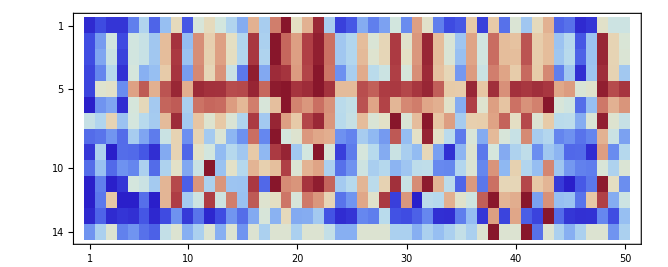

```mathematica
MatValAdd = Join[
Table[Flatten[{SSRel[[i]][[OrderRf]]/Max[SSRel[[i]][[Nets]]]}],{i,SigSS}],
Table[Flatten[{GraphRel[[i]][[OrderRf]]/Max[GraphRel[[i]][[Nets]]]}],{i,SigGraph}]
];
MatrixPlot[MatValAdd, ColorFunction->"ThermometerColors",ColorFunctionScaling->False]
```

Adding sum and Rf

```mathematica
SumVal = Total[MatVal,{1}]/Max[Total[MatVal,{1}]];
SpearmanRankTest[SumVal,DelInfo[[10]][[OrderRf]],"TestDataTable"]
PSum = SpearmanRankTest[SumVal,DelInfo[[10]][[OrderRf]],"PValue"];
```

| Statistic | P-Value
Spearman Rank | 0.389038 | 0.00523411

```mathematica
MatAll = MatrixPlot[Append[Append[MatVal,Flatten[{SumVal}]],Flatten[{DelInfo[[10]][[OrderRf]]}]], ColorFunction->"ThermometerColors",ColorFunctionScaling->False, PlotLegends->Automatic]
```

-Graphics-

```mathematica
Flatten[{DelInfo[[10]][[OrderRf]]}]
```

{0.,0.26666666666666674,0.434782608695652152,0.499999999999999838,0.518518518518518455,0.739130434782608651,0.782608695652173707,0.809523809523809489,0.862068965517241324,0.950000000000000175,0.960000000000000137,0.964285714285714137,0.965517241379310465,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
PvalsSig=Flatten[{SSCorr[[2]][[SigSS]], GraphCorr[[2]][[SigGraph]], PSum}];
MatrixPlot[Transpose[{PvalsSig}],ColorFunction->Hue, PlotLegends->Automatic]
```

-Graphics-

# Node degree vs sensor score

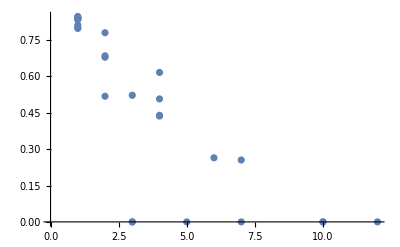
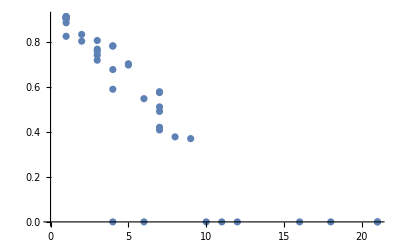
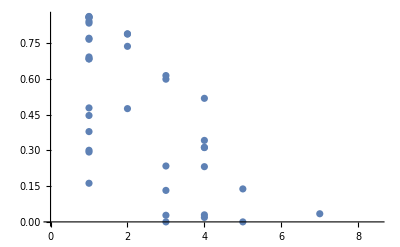
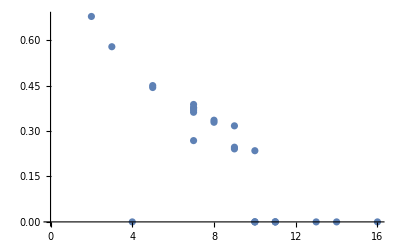
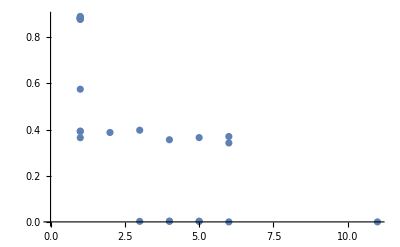
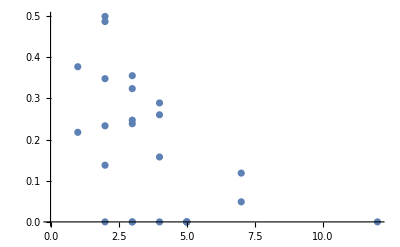
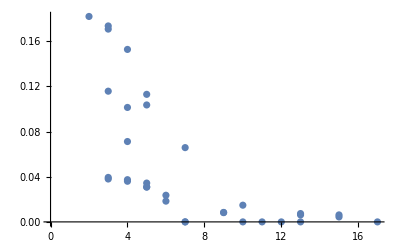
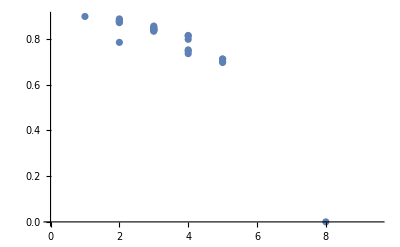
{{M_SD_001, | Statistic | P-Value
Spearman Rank | -0.90287 | 5.00162×10^-11,-Graphics-},{M_SD_002, | Statistic | P-Value
Spearman Rank | -0.930629 | 3.54337×10^-18,-Graphics-},{M_SD_003, | Statistic | P-Value
Spearman Rank | -0.737846 | 3.70893×10^-8,-Graphics-},{M_SD_008, | Statistic | P-Value
Spearman Rank | -0.830532 | 1.51605×10^-7,-Graphics-},{M_SD_009, | Statistic | P-Value
Spearman Rank | -0.813198 | 7.77402×10^-7,-Graphics-},{M_SD_011, | Statistic | P-Value
Spearman Rank | -0.557346 | 0.00379903,-Graphics-},{M_SD_014, | Statistic | P-Value
Spearman Rank | -0.858266 | 1.71228×10^-10,-Graphics-},{M_SD_015, | Statistic | P-Value
Spearman Rank | -0.933162 | 7.19833×10^-15,-Graphics-},{M_SD_017, | Statistic | P-Value
Spearman Rank | -0.922628 | 1.42857×10^-10,-Graphics-},{M_SD_021, | Statistic | P-Value
Spearman Rank | -0.635693 | 2.06652×10^-6,-Graphics-},{M_SD_023, | Statistic | P-Value
Spearman Rank | -0.730602 | 0.0000753242,-Graphics-},{M_SD_031, | Statistic | P-Value
Spearman Rank | -0.710311 | 1.08764×10^-8,-Graphics-},{M_SD_032, | Statistic | P-Value
Spearman Rank | -0.911824 | 1.42359×10^-9,-Graphics-},{M_SD_033, | Statistic | P-Value
Spearman Rank | -0.714729 | 0.0000870289,-Graphics-},{M_SD_010, | Statistic | P-Value
Spearman Rank | -0.906814 | 6.08691×10^-25,-Graphics-},{M_SD_012, | Statistic | P-Value
Spearman Rank | -0.870218 | 1.00109×10^-20,-Graphics-},{M_SD_013, | Statistic | P-Value
Spearman Rank | -0.771625 | 5.38466×10^-12,-Graphics-},{M_SD_020, | Statistic | P-Value
Spearman Rank | -0.909015 | 6.01951×10^-23,-Graphics-},{M_SD_024, | Statistic | P-Value
Spearman Rank | -0.694727 | 0.000963249,-Graphics-},{M_SD_025, | Statistic | P-Value
Spearman Rank | -0.628371 | 0.0214445,-Graphics-},{M_SD_026, | Statistic | P-Value
Spearman Rank | -0.956183 | 0.00283785,-Graphics-},{M_SD_027, | Statistic | P-Value
Spearman Rank | -0.960929 | 3.3604×10^-9,-Graphics-},{M_SD_028, | Statistic | P-Value
Spearman Rank | -0.71354 | 0.00616636,-Graphics-},{M_SD_029, | Statistic | P-Value
Spearman Rank | -0.933785 | 0.000230453,-Graphics-},{M_SD_030, | Statistic | P-Value
Spearman Rank | -0.819582 | 0.00685133,-Graphics-},{11sp_M_PL_069_03, | Statistic | P-Value
Spearman Rank | -0.780318 | 0.00460243,-Graphics-},{22sp_M_PL_036, | Statistic | P-Value
Spearman Rank | -0.816771 | 3.52732×10^-6,-Graphics-},{29sp_M_PL_069_01, | Statistic | P-Value
Spearman Rank | -0.696834 | 0.000154757,-Graphics-},{36sp_M_PL_067, | Statistic | P-Value
Spearman Rank | -0.877252 | 2.23588×10^-12,-Graphics-},{40sp_M_PL_032, | Statistic | P-Value
Spearman Rank | -0.830212 | 3.47534×10^-11,-Graphics-},{49sp_M_PL_050, | Statistic | P-Value
Spearman Rank | -0.789988 | 1.49789×10^-11,-Graphics-},{52sp_M_PL_071, | Statistic | P-Value
Spearman Rank | -0.62989 | 5.64067×10^-7,-Graphics-},{57sp_M_PL_025, | Statistic | P-Value
Spearman Rank | -0.772571 | 1.93513×10^-12,-Graphics-},{61sp_M_PL_003, | Statistic | P-Value
Spearman Rank | -0.849928 | 4.61888×10^-18,-Graphics-},{68sp_M_PL_039, | Statistic | P-Value
Spearman Rank | -0.790862 | 1.03286×10^-15,-Graphics-},{78sp_M_PL_006, | Statistic | P-Value
Spearman Rank | -0.748858 | 3.18472×10^-15,-Graphics-},{M_PL_008, | Statistic | P-Value
Spearman Rank | -0.883455 | 4.35531×10^-17,-Graphics-},{M_PL_011, | Statistic | P-Value
Spearman Rank | -0.81258 | 2.62866×10^-7,-Graphics-},{M_PL_013, | Statistic | P-Value
Spearman Rank | -0.748286 | 7.80252×10^-13,-Graphics-},{M_PL_033, | Statistic | P-Value
Spearman Rank | -0.721016 | 1.09022×10^-8,-Graphics-},{M_PL_037, | Statistic | P-Value
Spearman Rank | -0.86593 | 4.74448×10^-16,-Graphics-},{M_PL_038, | Statistic | P-Value
Spearman Rank | -0.8396 | 2.5687×10^-14,-Graphics-},{M_PL_046, | Statistic | P-Value
Spearman Rank | -0.894943 | 5.44987×10^-22,-Graphics-},{M_PL_059, | Statistic | P-Value
Spearman Rank | -0.877977 | 3.80694×10^-9,-Graphics-},{M_PL_063, | Statistic | P-Value
Spearman Rank | -0.890301 | 7.43793×10^-23,-Graphics-},{M_PL_064, | Statistic | P-Value
Spearman Rank | -0.618863 | 0.00213608,-Graphics-},{M_PL_065, | Statistic | P-Value
Spearman Rank | -0.914182 | 6.758×10^-11,-Graphics-},{M_PL_066, | Statistic | P-Value
Spearman Rank | -0.812614 | 1.75722×10^-9,-Graphics-},{M_PL_068, | Statistic | P-Value
Spearman Rank | -0.793692 | 1.0009×10^-9,-Graphics-},{M_PL_069_02, | Statistic | P-Value
Spearman Rank | -0.776955 | 0.00107822,-Graphics-},{M_PL_070, | Statistic | P-Value
Spearman Rank | 0.160401 | 0.552898,-Graphics-}}

```mathematica
Table[{i,fall[[i]],SpearmanRankTest[DegC[[i]],SensorScore[[i]],"TestDataTable"],ListPlot[Transpose@{DegC[[i]],SensorScore[[i]]}]},{i,Length[SensorScore]}]
```

# Older test

```mathematica
(*posNon1O = posNon1[[Ordering[DelInf[[10]][[posNon1]]]]];
valNon1O=DelInf[[10]][[posNon1O]];*)
```

```mathematica
posNon1O = Range[1,Length[DelInfo[[10]]]];
valNon1O=DelInfo[[10]];
```

```mathematica
OrderEW = Ordering[DelInfo[[10]]][[Flatten[{1,2,Range[4,51]}]]];
valNon1O = DelInfo[[10]][[OrderEW]];
posNon1O = OrderEW;
```

```mathematica
valMatrix = {
(*2*)SetSize[[OrderEW]]/Max[SetSize],
(*3*)RelSetSize[[OrderEW]]/Max[RelSetSize], 
(*4*)AnPlantDisp[[OrderEW]]/Max[AnPlantDisp],
(*5*)VarEW[[OrderEW]]/Max[VarEW],
(*6*)MaxEW[[OrderEW]]/Max[MaxEW],
 (*7*)MedEW[[OrderEW]]/Max[MedEW],
 (*8*)VarDeg[[OrderEW]]/Max[VarDeg], 
(*9*)(1/MeanDeg[[OrderEW]])/Max[(1/MeanDeg)], 
(*10*)(1/Connectance[[OrderEW]])/Max[1/Connectance],
(*11*)MeanSS[[OrderEW]]/Max[MeanSS],
(*12*)MaxSS[[OrderEW]]/Max[MaxSS],
(*13*)VarSS[[OrderEW]]/Max[VarSS]};
```

| Statistic | P-Value
Spearman Rank | 0.340099 | 0.014612

| Statistic | P-Value
Kendall τ | 0.269324 | 0.0143869

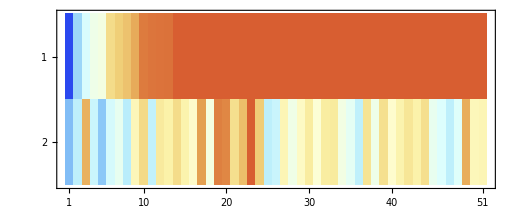

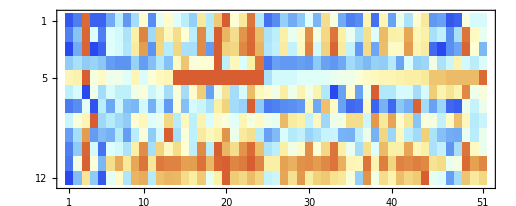

```mathematica
tot=Total[valMatrix,{1}];
totalMatrix = {
(*1*)DelInfo[[10]][[OrderEW]]/Max[DelInfo[[10]]],
(*2*) tot/Max[tot]
};
SpearmanRankTest[DelInfo[[10]][[OrderEW]]/Max[DelInfo[[10]]], tot/Max[tot],"TestDataTable"]
KendallTauTest[DelInfo[[10]][[OrderEW]]/Max[DelInfo[[10]]], tot/Max[tot],"TestDataTable"]
MatrixPlot[totalMatrix, ColorFunction->"LightTemperatureMap", ColorFunctionScaling->False]
MatrixPlot[valMatrix, ColorFunction->"LightTemperatureMap",ColorFunctionScaling->False]
```

```mathematica
valMatrix2 = {
 (*1MedEW[[OrderEW]]/Max[MedEW],
(*2*)VarEW[[OrderEW]]/Max[VarEW],*)
SkewDeg[[OrderEW]]/Max[SkewDeg],
(*3*)VarSS[[OrderEW]]/Max[VarSS],
(*4*)MeanSS[[OrderEW]]/Max[MeanSS],
(*5*)RelSetSize[[OrderEW]]/Max[RelSetSize],
(*6*)MaxSS[[OrderEW]]/Max[MaxSS], 
(*7*)AnPlantDisp[[OrderEW]]/Max[AnPlantDisp],
(*8*)(1/Connectance[[OrderEW]])/Max[1/Connectance],
(*9MaxEW[[OrderEW]]/Max[MaxEW],*)
(*10*)(1/MeanDeg[[OrderEW]])/Max[(1/MeanDeg)], 
 (*11*)VarDeg[[OrderEW]]/Max[VarDeg]};
MatrixPlot[valMatrix2,ColorFunction->"ThermometerColors", ColorFunctionScaling->False];
tot2=Total[valMatrix2,{1}];
totalMatrix2= Append[valMatrix2,
(*2*) tot2/Max[tot2]
];

totalMatrix3 = Append[totalMatrix2,DelInfo[[10]][[OrderEW]]/Max[DelInfo[[10]]]];
SpearmanRankTest[DelInfo[[10]][[OrderEW]], tot2,"TestDataTable"]
MatrixPlot[totalMatrix3, ColorFunction->"ThermometerColors", ColorFunctionScaling->False, PlotLegends->Automatic]
```

| Statistic | P-Value
Spearman Rank | 0.376922 | 0.0069728

-Graphics-

Median EWS

```mathematica
MedEW = Table[Median[Detect[[i]]],{i,Length[Detect]}];
```

```mathematica
SpearmanRankTest[valNon1O,MedEW[[posNon1O]],"TestData"]
ListPlot[Transpose@{valNon1O,MedEW[[posNon1O]]}, PlotLabel->"Rf vs Median EWS"];
```

{0.272145,0.0558838}

Variance of EWS

```mathematica
VarEW = Table[Variance[Detect[[i]]],{i,Length[Detect]}];
```

```mathematica
SpearmanRankTest[valNon1O,VarEW[[posNon1O]],"TestData"]
ListPlot[Transpose@{valNon1O,VarEW[[posNon1O]]}, PlotLabel->"Rf vs Variance EWS"];
```

{0.313974,0.0263877}

Var SS

```mathematica
SpearmanRankTest[valNon1O,VarSS[[posNon1O]],"TestData"]
ListPlot[Transpose@{valNon1O,VarSS[[posNon1O]]}, PlotLabel->"Rf vs Mean SS"];
```

{0.311089,0.0278796}

Median SS  (not included)

```mathematica
SpearmanRankTest[valNon1O,MedSS[[posNon1O]],"TestData"]
```

{0.329943,0.0192844}

Mean SS

```mathematica
SpearmanRankTest[valNon1O,MeanSS[[posNon1O]],"TestData"]
ListPlot[Transpose@{valNon1O,MeanSS[[posNon1O]]}, PlotLabel->"Rf vs Mean SS"];
```

{0.354501,0.0115395}

Relative set size

```mathematica
SpearmanRankTest[valNon1O,RelSetSize[[posNon1O]],"TestData"]
ListPlot[Transpose@{valNon1O,RelSetSize[[posNon1O]]}, PlotLabel->"Rf vs Relative Set Size"];
```

{0.351037,0.0124359}

Max SS

```mathematica
SpearmanRankTest[valNon1O,MaxSS[[posNon1O]],"TestData"]
ListPlot[Transpose@{valNon1O,MaxSS[[posNon1O]]}, PlotLabel->"Rf vs Max SS"];
```

{0.34641,0.0137257}

Plant animal disparity

```mathematica
SpearmanRankTest[valNon1O,AnPlantDisp[[posNon1O]],"TestData"]
ListPlot[Transpose@{valNon1O,AnPlantDisp[[posNon1O]]}, PlotLabel->"Rf vs Plant-animal disparity"];
```

{0.324097,0.0216695}

Connectance

```mathematica
SpearmanRankTest[valNon1O,1/Connectance[[posNon1O]],"TestData"]
ListPlot[Transpose@{valNon1O,1/Connectance[[posNon1O]]}, PlotLabel->"Rf vs Connectance"];
```

{0.312115,0.0273413}

Set size

```mathematica
SpearmanRankTest[valNon1O,SetSize[[posNon1O]],"TestData"]
ListPlot[Transpose@{valNon1O,SetSize[[posNon1O]]}, PlotLabel->"Rf vs Set Size"];
```

{0.310174,0.0283676}

Max EWS

```mathematica
MaxEW = Table[Max[Detect[[i]]],{i,Length[Detect]}];
```

```mathematica
SpearmanRankTest[valNon1O,MaxEW[[posNon1O]],"TestData"]
ListPlot[Transpose@{valNon1O,MaxEW[[posNon1O]]}, PlotLabel->"Rf vs Max EWS"];
```

{0.277838,0.0507515}

Mean degree

```mathematica
MeanDeg = Table[Mean[DegC[[i]]],{i,Length[Detect]}];
```

```mathematica
SpearmanRankTest[valNon1O,1/MeanDeg[[posNon1O]],"TestData"]
ListPlot[Transpose@{valNon1O,1/MeanDeg[[posNon1O]]}, PlotLabel->"Rf vs Mean Degree Cent"];
```

{0.198892,0.166148}

Variance Degree

```mathematica
VarDeg = Table[Variance[DegC[[i]]],{i,Length[Detect]}];
```

```mathematica
SpearmanRankTest[valNon1O,VarDeg[[posNon1O]],"TestData"]
ListPlot[Transpose@{valNon1O,VarDeg[[posNon1O]]}, PlotLabel->"Rf vs Variance Degree Cent"];
```

{0.157692,0.274083}

```mathematica
SkewDeg =N[ Table[Skewness[DegC[[i]]],{i,Length[Detect]}]]
```

{1.294,1.47344,1.93376,0.155325,1.30743,1.82735,0.730438,2.25579,0.706613,1.66247,1.76893,3.40603,2.08207,0.673661,1.47902,1.43966,0.548361,1.919,0.861875,0.706203,0.,1.18263,0.32526,0.823754,0.125677,0.164501,1.40891,2.48668,3.96357,3.21703,1.83557,4.93985,2.73799,2.4167,1.65712,5.20686,1.67378,1.41326,4.48479,0.990008,2.4707,2.41313,1.01818,0.694618,5.38662,1.95511,2.56859,3.14429,2.89914,1.30145,0.238711}

```mathematica
SpearmanRankTest[valNon1O,SkewDeg[[posNon1O]],"TestData"]
ListPlot[Transpose@{valNon1O,VarDeg[[posNon1O]]}, PlotLabel->"Rf vs Variance Degree Cent"];
```

{0.318012,0.0244116}

# Sensor Score - EW Score density distribution

```mathematica
dScore = Table[Detect[[i]]/Max[Detect[[i]]],{i,Length[Detect]}]; (*EW-score with full competition*)
dScore0 = Table[Detect0[[i]]/Max[Detect0[[i]]],{i,Length[Detect0]}]; (*EW-score with no competition*)
FSensorScore=Flatten[SensorScore];
FDetectScore = Flatten[dScore]; (*EW-score with full competition (flattened) *)
FDetectScore0 = Flatten[dScore0];
PairDetectSensor = Transpose@{FDetectScore,FSensorScore};
PairDetectSensorm = Transpose@{-1*Flatten[dScore ],Flatten[SensorScore]};
```

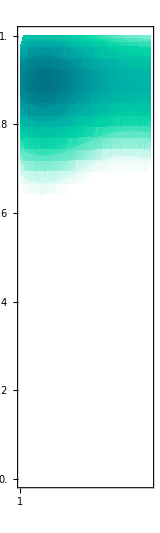
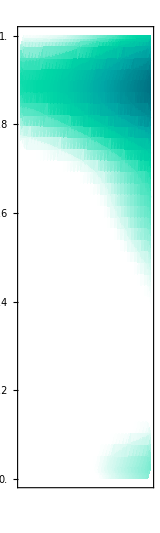
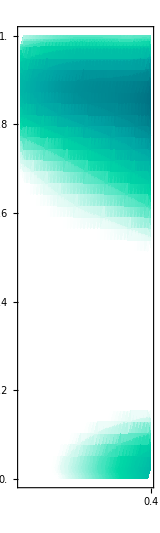
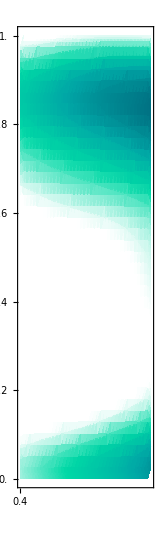
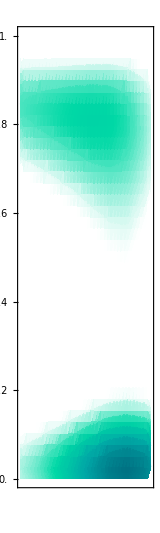

```mathematica
Table[SmoothDensityHistogram[PairDetectSensorm,Automatic, "Intensity",ColorFunction->(Blend[{White,White, RGBColor[0, 0.85, 0.65],RGBColor[0, 0.65, 0.65],RGBColor[0, 0.44, 0.51]},Rescale[#,{0,1}]]&),FrameTicks->{{Range[0,1,0.2],None}, {{{-1,1},{-.9,.9},{-.8,.8},{-.7,.7}, {-.6,.6},{-.5,.5}, {-.4,.4},{-.3,.3}, {-.2,.2},{-.1,.1},{0,0}},None}},FrameTicksStyle->12,
ColorFunctionScaling->True,
 Mesh->6,
 PlotLegends->Placed[Automatic,Above],PlotRange->{{i,i+.2},{0,1}},AspectRatio->5/1.5,ImageSize->{160,350}],{i,{-1,-.8,-.6,-.4,-.2}}]
```

## probability of finding a given early - warning score

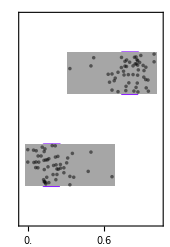

```mathematica
ClearAll[cef2]
bins={0,0.5,1};
datatemp=Table[
HistogramList[d,{bins},"Probability"]⟦2⟧
,{d, dScore}];
cef2={
EdgeForm[],FaceForm[],ChartElementData["BoxWhisker"][##]/.{l_Line:>{RGBColor[0.55, 0.13, 1],l},GrayLevel[0]->RGBColor[0.55, 0.13, 1]},ChartElementData["PointDensity","PointStyle"->Directive[Opacity[0.5],PointSize[0.015],Black]][##]}&;

fig1=BoxWhiskerChart[Reverse@Transpose@datatemp,
Frame->True,
ChartElementFunction->cef2,
AspectRatio->0.8GoldenRatio,
FrameTicksStyle->12,
FrameTicks->{{All,All},{Range[0,1,0.2],None}},
ChartStyle->Directive[EdgeForm[Black], Gray],
ImageSize->170,
BarOrigin->Left];

options={{
{"MedianMarker",1,None},
{"MeanMarker",1,Directive[Thickness[.01],RGBColor[0.55, 0.13, 1]]},
{"Fences",1,Directive[Thickness[.01],RGBColor[0.55, 0.13, 1]]},
{"Whiskers",Directive[Thickness[.01],CapForm["Butt"],RGBColor[0.55, 0.13, 1]]}},
ChartStyle->Directive[EdgeForm[{RGBColor[0.55, 0.13, 1],Thickness[0.01]}], White],
ChartElementFunction->ChartElementDataFunction["BoxWhisker"]};

fig2=BoxWhiskerChart[Reverse@Transpose@datatemp,##&@@options,
Frame->True,
AspectRatio->0.9GoldenRatio,
FrameTicksStyle->12,
FrameTicks->{{All,All},{Range[0,1,0.2],None}},
ImageSize->170,
BarOrigin->Left];

fig3 = Show[{fig2, fig1}]
```